```mathematica
Clear[a,b,c,d,z,fRab];
fRab:=b*d-(b+z)/(b+d*z^2)+(b*z^4)/(b+c)+b*z^2/(a+z)+(z*(b+a*z^2))/(b+z^3);

Denominator[Part[fRab,2]]

StringLength["Part[fRab,{2,3,4}]"]
```

b+c

18

```mathematica
Clear[d,w,z];
(#1+#2^4)^3-#3^3+(#2^3+#3)^2[d,w,z]//InputForm
```

(#1 + #2^4)^3 - #3^3 + (#2^3 + #3)^2[d, w, z]

```mathematica
ToString["Function[(#1+#2^4)^3-#3^3+(#2^3+#3)^2]"]
```

Function[(#1+#2^4)^3-#3^3+(#2^3+#3)^2]

```mathematica
Function[x,Surd[x,7]][62748517]
#^(1/7)&[62748517]
```

13

13

```mathematica
Clear[a,b,c,d,x];
fRab:=a*x^3-(c+x^3)/(d+x^2)+(a+x^3)/(d+x^4);
Position[fRab,x^3,3]
InputForm[fRab]
```

{{1,2},{2,3,2},{3,1,2}}

a*x^3 - (c + x^3)/(d + x^2) + (a + x^3)/(d + x^4)

```mathematica
Clear[a,b,c,d,z];
fRab:=a*z^3+b*z^2-c/(d+z)+z/(d+z)+Tan[z];
Part[fRab,{2,3,4}]//InputForm
```

a*z^3 - c/(d + z) + z/(d + z)

```mathematica
StringLength["PlotRangeClipping"]
```

17

```mathematica
Clear[a,b,c,d,z];
fRab:=a*z+b*z^2-c/(d+z)+z/(d+z)+Cos[z];
Part[fRab,Span[2,4]]//InputForm
```

b*z^2 - c/(d + z) + z/(d + z)

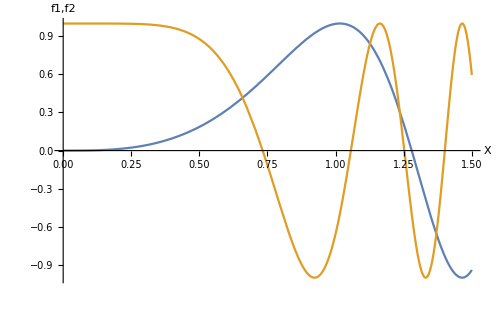

```mathematica
aX="X";
aY="f1,f2";
f1[x_]:=Sin[1.5*x^3];
f2[x_]:=Cos[4*x^3];
grf1=Plot[{f1[x],f2[x]},{x,0,3/2},ImageSize->500,AxesLabel->{aX,Rotate[aY,60Degree]},AxesStyle->Directive[18]]
```

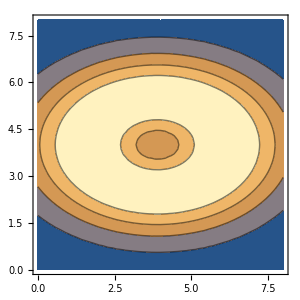
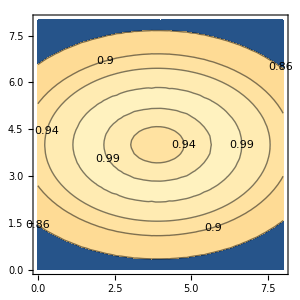

```mathematica
fXY[x_,y_]:=Sin[1+E^(-(x/3-1.3)^2-(y/2-2)^2)];
grXY1=ContourPlot[fXY[x,y],{x,0,8},{y,0,8},ImageSize->300,Contours->4];
grXY2=ContourPlot[fXY[x,y],{x,0,8},{y,0,8},ImageSize->300,Contours->{0.99,0.94,0.9,0.86},ContourLabels->All]; Row[{grXY1,grXY2},Spacer[20]]
```

```mathematica
TextCell
```

TemplateEvaluate